## Packages and definitions

```mathematica
(* Load the Package *)
<<QuantumWalks`
```

```mathematica
ResourceFunction["AddMatplotlibColors"][]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

```mathematica
createFrame[stepIndex_] := Module[
    {plotData, currentProbs, exactAspectRatio},
    
    currentProbs = probabilityDistributions[[stepIndex]];
    plotData = MapThread[Append, {coords, currentProbs}];
    
    (* Calculamos la relación de aspecto física estricta (Alto / Ancho) *)
    exactAspectRatio = (radiusR + 1) / (lengthL + radiusR + 1);
    
    ListDensityPlot[plotData,
        ColorFunctionScaling -> False,
        
        (* Invertimos Magma: 1 - valor_normalizado *)
        ColorFunction -> Function[prob, 
            If[prob <= probMin, 
                White, 
                ColorData["Magma"][1 - Clip[(Log10[prob] - logPMin) / (logPMax - logPMin), {0, 1}]]
            ]
        ],
        
        PlotRange -> {
            {-(lengthL + radiusR + 1), lengthL + radiusR + 1}, 
            {-(radiusR + 1), radiusR + 1}, 
            {0, maxProb}
        },
        Mesh -> False,
        InterpolationOrder -> 0, 
        FrameLabel -> {"X", "Y"},
        PlotLabel -> Style["Full Bunimovich Stadium | t = " <> ToString[stepIndex - 1], 16, Bold],
        ImageSize -> Large,
        
        (* Retornamos a un fondo blanco y ejes negros *)
        Background -> White, 
        LabelStyle -> Directive[Black, 20], 
        AxesStyle -> Black,
        FrameStyle -> Black,
        
        PlotLegends -> Placed[
            BarLegend[{
                (* La leyenda también debe usar la función invertida *)
                Function[logProb, 
                    ColorData["Magma"][1 - Clip[(logProb - logPMin) / (logPMax - logPMin), {0, 1}]]
                ], 
                {logPMin, logPMax}
            }, 
            Ticks -> ({#, Superscript[10, #]} & /@ Range[Round[logPMin], Ceiling[logPMax]]),
            LegendLabel -> Style["Probability", 14, Black], 
            LabelStyle -> Directive[Black, 14],
            LegendMarkerSize -> 300], 
            Right
        ],
        
        (* Obligamos a Mathematica a usar la proporción física exacta *)
        AspectRatio -> exactAspectRatio,
        
        RegionFunction -> Function[{x, y, prob},
            Abs[y] <= If[Abs[x] <= lengthL, 
                          radiusR, 
                          Sqrt[Max[0, radiusR^2 - (Abs[x] - lengthL)^2]]
                      ]
        ],
        
        (* Fronteras del estadio de vuelta a negro para hacer contraste *)
        Epilog -> {
            Directive[Thick, Black],
            Line[{{-lengthL, radiusR}, {lengthL, radiusR}}],   
            Line[{{-lengthL, -radiusR}, {lengthL, -radiusR}}], 
            Circle[{lengthL, 0}, radiusR, {-Pi/2, Pi/2}],      
            Circle[{-lengthL, 0}, radiusR, {Pi/2, 3 Pi/2}]     
        }
    ]
];
```

## Bunimovich

### 4D coin

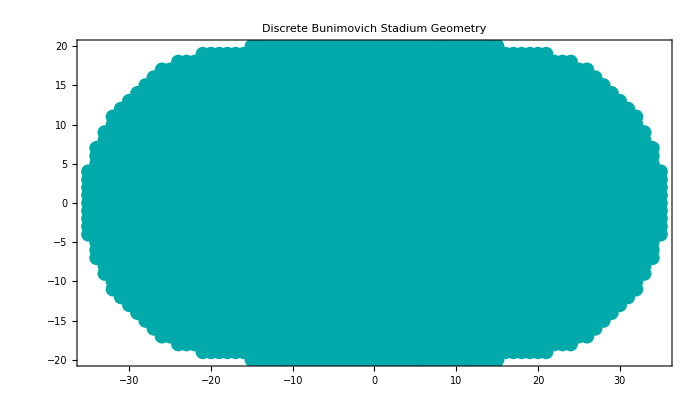

```mathematica
(* 1. Define Geometry: Full Bunimovich Stadium *)
radiusR = 20;
lengthL = 15;
gridData = GenerateFullStadiumBasis[lengthL, radiusR];
dimSpace = gridData["Dimension"];

(* Extract coordinates and plot the spatial grid *)
stadiumPlot = ListPlot[
    gridData["Coords"],
    AspectRatio -> Automatic,
    PlotStyle -> Directive[PointSize[0.015], Darker[Cyan]],
    Frame -> True,
    Axes -> False,
    PlotLabel -> "Discrete Bunimovich Stadium Geometry",
LabelStyle->Directive[Black,23],
    ImageSize->700
]
```

```mathematica
(* 2. Operators: 4D Shift and Global Grover Coin *)
(* Constructing the 4-state shift operator and the tensor-product coin *)
shiftOp = BuildShiftOperators[gridData, CoinDimension -> 4];
coinOp = KroneckerProduct[
    IdentityMatrix[dimSpace, SparseArray], 
    GeneralizedGroverCoin[Pi/4]
];
unitaryStep = shiftOp . coinOp;
```

```mathematica
(* 3. Symmetry Reduction: Even-Even Sector (A1) *)
(* Projecting the full unitary onto the C2v A1 subspace to reduce dimensionality *)
isometryV = BuildSymmetryIsometry[gridData, "A1"];
unitaryRed = Chop[ConjugateTranspose[isometryV] . unitaryStep . isometryV];
```

```mathematica
(* 4. State Initialization (Localized in the reduced space) *)
dimRed = Dimensions[unitaryRed][[1]];
initialStateRed = SparseArray[{1 -> 1.0 + 0.I}, dimRed];
```

```mathematica
(* 5. Time Evolution (t = 0 to 10) *)
tMax=1000;
evolutionRed = NestList[unitaryRed . # &, initialStateRed, tMax];

(* Project the A1 evolution back into the full dimensional Hilbert space *)
evolutionFull = isometryV . # & /@ evolutionRed;

(* Extract raw spatial coordinates for the plotting function *)
coords = gridData["Coords"];
dimSpace = gridData["Dimension"];

(* Compute spatial probabilities by tracing out the 4 internal coin states *)
probabilityDistributions = Table[
    Total[Abs[stateFull[[4*(i-1)+1 ;; 4*i]]]^2],
    {stateFull, evolutionFull},
    {i, 1, dimSpace}
];
```

```mathematica
(* 6. Animation Generation Setup (Modified for Full Stadium) *)
maxProb = Max[probabilityDistributions];
probMin = 2*10.^-10; (* Threshold to avoid Log[0] *)
logPMin = Log10[probMin];
logPMax = Log10[maxProb];

(* 7. Execute Animation *)
frames = Table[createFrame[i], {i, 1, Length[probabilityDistributions]}];
ListAnimate[frames,2]
```

```mathematica
Min[Select[Chop@probabilityDistributions[[-1]],#>0.&]]
```

2.43224×10^-6

```mathematica
Select[Chop@Flatten[probabilityDistributions],10.^-5>#>10.^-10&]//Length
```

699

```mathematica
Position[probabilityDistributions[[1]],x_/;x>0.]
```

{{1262}}

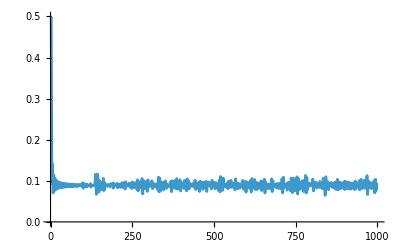

```mathematica
ListLinePlot[{{#,probabilityDistributions[[#,1303]]}&/@Range[2,tMax,2]},
PlotRange->All
]
```

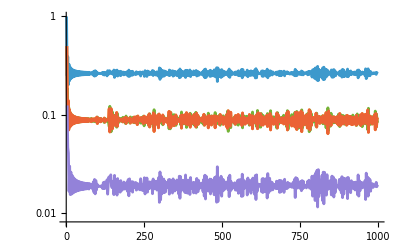

```mathematica
ListLogPlot[{
{#,probabilityDistributions[[#,1262]]}&/@Range[1,tMax,2],{#,probabilityDistributions[[#,1303]]}&/@Range[2,tMax,2],
{#,probabilityDistributions[[#,1263]]}&/@Range[2,tMax,2],
{#,probabilityDistributions[[#,1221]]}&/@Range[2,tMax,2],
{#,probabilityDistributions[[#,1304]]}&/@Range[1,tMax,2]
},
PlotRange->All,
Joined->True
]
```

```mathematica
(* Define the destination path in the same folder as your current notebook *)
videoPath = FileNameJoin[{NotebookDirectory[], "BunimovichStadiumDynamics.mp4"}]
```

/home/jadeleon/Documents/libs/QuantumWalks/UsageExamples/BunimovichStadiumDynamics.mp4

```mathematica
(* Export the sequence of frames directly to MP4 *)
Export[
    videoPath, 
    frames, 
    {"MP4","VideoEncoding"->"H264","FrameRate"->1}
];

Print["Video successfully exported to: ", videoPath];
```

Export::inselem: There are insufficient elements to export to MP4 format.

Video successfully exported to: /home/jadeleon/Documents/libs/QuantumWalks/UsageExamples/BunimovichStadiumDynamics.mp4

```mathematica
rasterizedFrames=Rasterize[#,"Image",ImageResolution->144]&/@frames;
```

```mathematica
Do[Export[FileNameJoin@{DirectoryName[videoPath],StringTemplate["frame_``.png"][IntegerString[i,10,4]]},rasterizedFrames[[i]]],{i,Length[rasterizedFrames]}]
```

### 2D-coin (Alonso-Lobo)

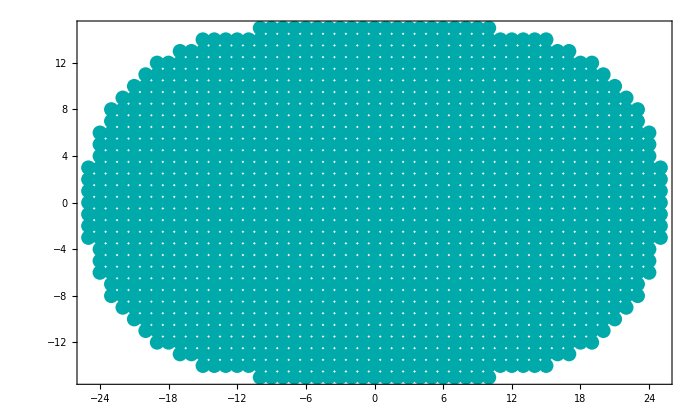

```mathematica
(* 1. Define Geometry: Full Bunimovich Stadium *)
radiusR = 15;
lengthL = 10;
gridData = GenerateFullStadiumBasis[lengthL, radiusR];
dimSpace = gridData["Dimension"];

(* Extract coordinates and plot the spatial grid *)
stadiumPlot = ListPlot[
    gridData["Coords"],
    AspectRatio -> Automatic,
    PlotStyle -> Directive[PointSize[0.015], Darker[Cyan]],
    Frame -> True,
    Axes -> False,
LabelStyle->Directive[Black,23],
    ImageSize->700
]
```

```mathematica
(* 2. Operators: 4D Shift and Global Grover Coin *)
(* Constructing the 4-state shift operator and the tensor-product coin *)
{Sx,Sy} = BuildShiftOperators[gridData];
{α,β}={Pi/4.,Pi/3.};{coinA,coinB}=Coin[#,dimSpace]&/@{α,β};
unitaryStep = Sx.coinB.Sy.coinA
```

SparseArray[…]

```mathematica
(* 3. State Initialization (Localized in the reduced space) *)
initialStateRed = SparseArray[{2*gridData["Mapping"][{0,0}]-1->1.},2*dimSpace];
```

```mathematica
(* 4. Time Evolution (t = 0 to 10) *)
tMax=100;
evolutionFull = NestList[unitaryStep . # &, initialStateRed, tMax];

(* Extract raw spatial coordinates for the plotting function *)
coords = gridData["Coords"];
dimSpace = gridData["Dimension"];

(* Compute spatial probabilities by tracing out the 4 internal coin states *)
probabilityDistributions = Table[
    Total[Abs[stateFull[[2*(i-1)+1 ;; 2*i]]]^2],
    {stateFull, evolutionFull},
    {i, 1, dimSpace}
];
```

```mathematica
(* 5. Animation Generation Setup (Modified for Full Stadium) *)
maxProb = Max[probabilityDistributions];
probMin = 2*10.^-10; (* Threshold to avoid Log[0] *)
logPMin = Log10[probMin];
logPMax = Log10[maxProb];
```

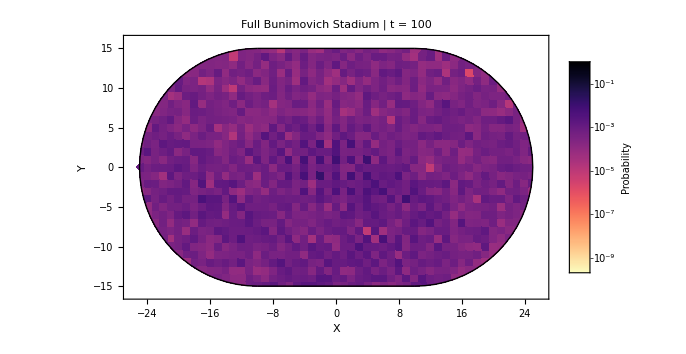

```mathematica
createFrame[101]
```

```mathematica
(* Execute Frame Generation & Export *)
frames = Table[createFrame[i], {i, 1, Length[probabilityDistributions]}];
rasterizedFrames=Rasterize[#,"Image",ImageResolution->144]&/@frames;

Do[
	Export[
		FileNameJoin@{DirectoryName["/home/jadeleon/Documents/libs/QuantumWalks/UsageExamples"],StringTemplate["frame_``.png"][IntegerString[i,10,4]]},
		rasterizedFrames[[i]]
		],
{i,Length[rasterizedFrames]}]
```

DirectoryName::string: String expected at position 1 in DirectoryName[videoPath].

Export::chtype: The first argument FileNameJoin[{DirectoryName[videoPath],frame_0001.png}] is not a valid file specification.

Export::chtype: The first argument FileNameJoin[{DirectoryName[videoPath],frame_0002.png}] is not a valid file specification.

Export::chtype: The first argument FileNameJoin[{DirectoryName[videoPath],frame_0003.png}] is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

## Rectangular billiard

```mathematica
(* 1. Define Geometry: Rectangular Billiard *)
widthLx = 30;
heightLy = 15;
gridData = GenerateRectangleBasis[widthLx, heightLy];
dimSpace = gridData["Dimension"];
coords = gridData["Coords"];

(* 2. Operators: 4D Shift and Global Grover Coin *)
shiftOp = BuildShiftOperators[gridData, CoinDimension -> 4];
coinOp = KroneckerProduct[
    IdentityMatrix[dimSpace, SparseArray], 
    GeneralizedGroverCoin[Pi/4]
];
(* Calculate the unitary step for the full space *)
unitaryStep = Chop[shiftOp . coinOp];
```

Localized initial state:

```mathematica
(* 3. State Initialization (Centered in the rectangle) *)
(* We find the index of the geometric center to place our initial wave packet *)
centerCoord = {Round[widthLx / 2], Round[heightLy / 2]};
centerIndex = gridData["Mapping"][centerCoord];

(* Initializing in the "Up" state (Spin 1) at the center node *)
initialStateFull = SparseArray[{4 * (centerIndex - 1) + 1 -> 1.0 + 0.I}, 4 * dimSpace];
```

Gaussian initial state:

```mathematica
(* 1. Define Gaussian parameters *)
(* You can manually set centerCoord to any {x,y} valid for your chosen geometry *)
(* For the rectangle: centerCoord = {Round[widthLx / 2], Round[heightLy / 2]}; *)
(* For the cardioid: centerCoord = {-radiusR, 0}; *)
sigma = .5; (* Standard deviation / spread of the wavepacket *)

(* 2. Calculate spatial amplitudes *)
(* Amplitude decays as Exp[-r^2 / (4 * sigma^2)] so probability decays as Exp[-r^2 / (2 * sigma^2)] *)
centerCoord=Round[Mean[coords]];
gaussianAmplitudes = Map[
    Exp[-(EuclideanDistance[#, centerCoord]^2) / (4 * sigma^2)] &,
    gridData["Coords"]
];

(* 3. Map to the full 4D Coin Hilbert space *)
(* We place the Gaussian amplitude exclusively in the "Up" coin state (index 1) of each node *)
initialStateFull = SparseArray[
    Table[
        4 * (i - 1) + 1 -> gaussianAmplitudes[[i]] + 0.I,
        {i, 1, dimSpace}
    ],
    {4 * dimSpace}
];

(* 4. Enforce strict quantum normalization *)
initialStateFull = Normalize[initialStateFull];

(* ---------------------------------------------------------------------- *)
(* IMPORTANT: If you are running the Bunimovich Stadium or Cardioid code  *)
(* which uses symmetry reduction, you MUST keep this projection line to   *)
(* map the Gaussian down into the reduced A1/Even subspace:               *)
(* *)
(* initialStateRed = Normalize[Chop[ConjugateTranspose[isometryV] . initialStateFull]]; *)
(* ---------------------------------------------------------------------- *)
```

```mathematica
(* 4. Time Evolution (t = 0 to 15) *)
tMax=100;
evolutionFull = NestList[unitaryStep . # &, initialStateFull, tMax];

(* 5. Compute Probabilities (Tracing out the coin degrees of freedom) *)
probabilityDistributions = Table[
    Total[Abs[stateFull[[4*(i-1)+1 ;; 4*i]]]^2],
    {stateFull, evolutionFull},
    {i, 1, dimSpace}
];

(* 6. Animation Generation Setup *)
maxProb = Max[probabilityDistributions];
probMin = 2*10.^-9; 
logPMin = Log10[probMin];
logPMax = Log10[maxProb];

(* Correct Physical Aspect Ratio *)
exactAspectRatio = heightLy / widthLx;

createFrame[stepIndex_] := Module[
    {plotData, currentProbs},
    
    currentProbs = probabilityDistributions[[stepIndex]];
    plotData = MapThread[Append, {coords, currentProbs}];
    
    ListDensityPlot[plotData,
        ColorFunctionScaling -> False,
        ColorFunction -> Function[prob, 
            If[prob <= probMin, 
                White, 
                ColorData["Magma"][1 - Clip[(Log10[prob] - logPMin) / (logPMax - logPMin), {0, 1}]]
            ]
        ],
        PlotRange -> {{0, widthLx}, {0, heightLy}, {0, maxProb}},
        Mesh -> False,
        InterpolationOrder -> 0, 
        FrameLabel -> {"X", "Y"},
        PlotLabel -> Style["Rectangle Billiard | t = " <> ToString[stepIndex - 1], 16, Bold],
        ImageSize -> Large,
        Background -> White, 
        LabelStyle -> Directive[Black, 20], 
        AxesStyle -> Black,
        FrameStyle -> Black,
        
        PlotLegends -> Placed[
            BarLegend[{
                Function[logProb, 
                    ColorData["Magma"][1 - Clip[(logProb - logPMin) / (logPMax - logPMin), {0, 1}]]
                ], 
                {logPMin, logPMax}
            }, 
            Ticks -> ({#, Superscript[10, #]} & /@ Range[Round[logPMin], Ceiling[logPMax]]),
            LegendLabel -> Style["Probability", 14, Black], 
            LabelStyle -> Directive[Black, 14],
            LegendMarkerSize -> 300], 
            Right
        ],
        
        AspectRatio -> exactAspectRatio,
        
        (* Region constrained perfectly to the rectangle limits *)
        RegionFunction -> Function[{x, y, prob},
            0 <= x <= widthLx && 0 <= y <= heightLy
        ],
        
        (* Draw the simple rectangular boundaries *)
        Epilog -> {
            Directive[Thick, Black],
            Line[{{0, 0}, {widthLx, 0}, {widthLx, heightLy}, {0, heightLy}, {0, 0}}]
        }
    ]
];

(* 7. Execute Frame Generation *)
frames = Table[createFrame[i], {i, 1, Length[probabilityDistributions]}];
```

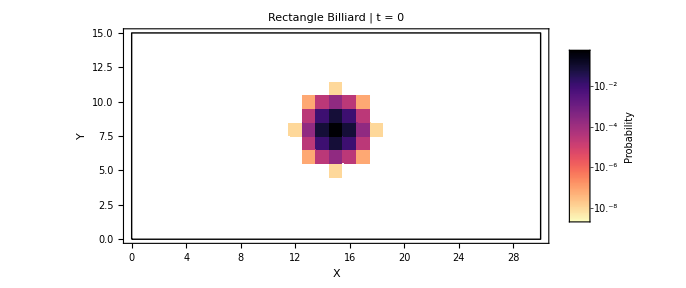

```mathematica
frames[[1]]
```

```mathematica
rasterizedFrames=Rasterize[#,"Image",ImageResolution->144]&/@frames;
```

```mathematica
Do[Export[FileNameJoin@{DirectoryName[videoPath],StringTemplate["frame_``.png"][IntegerString[i,10,4]]},rasterizedFrames[[i]]],{i,Length[rasterizedFrames]}]
```

## Cardioid

```mathematica
(* 1. Define Geometry: Cardioid Billiard *)
(* X range: [-4R, R], Y range: [-3R, 3R] *)
radiusR = 15;
gridData = GenerateCardioidBasis[radiusR];
dimSpace = gridData["Dimension"];
coords = gridData["Coords"];

(* 2. Operators: 4D Shift and Global Grover Coin *)
shiftOp = BuildShiftOperators[gridData, CoinDimension -> 4];
coinOp = KroneckerProduct[
    IdentityMatrix[dimSpace, SparseArray], 
    GeneralizedGroverCoin[Pi/4]
];
(* Calculate the unitary step for the full space *)
unitaryStepFull = Chop[shiftOp . coinOp];

(* 3. Symmetry Reduction (Even Parity / Cs Symmetry) *)
(* The cardioid is only symmetric across the X-axis (y -> -y). We project to the "Even" subspace *)
isometryV = BuildSymmetryIsometry[gridData, "Even"];
unitaryRed = Chop[ConjugateTranspose[isometryV] . unitaryStepFull . isometryV];
```

Localized initial state:

```mathematica
(* 4. State Initialization (Symmetric State) *)
(* We place the initial state on the symmetry axis so it intrinsically has even parity *)
centerCoord = {-radiusR, 0}; 
centerIndex = gridData["Mapping"][centerCoord];

(* Initializing in the "Up" state at the specified node in FULL space *)
initialStateFull = SparseArray[{4 * (centerIndex - 1) + 1 -> 1.0 + 0.I}, 4 * dimSpace];

(* Project the initial state down into the reduced subspace and normalize *)
initialStateRed = Normalize[Chop[ConjugateTranspose[isometryV] . initialStateFull]];
```

Gaussian initial state:

```mathematica
(* 1. Define Gaussian parameters *)
(* You can manually set centerCoord to any {x,y} valid for your chosen geometry *)
(* For the rectangle: centerCoord = {Round[widthLx / 2], Round[heightLy / 2]}; *)
(* For the cardioid: centerCoord = {-radiusR, 0}; *)
sigma = 1.; (* Standard deviation / spread of the wavepacket *)

(* 2. Calculate spatial amplitudes *)
(* Amplitude decays as Exp[-r^2 / (4 * sigma^2)] so probability decays as Exp[-r^2 / (2 * sigma^2)] *)
centerCoord=Round[Mean[coords]]+{0,10}
gaussianAmplitudes = Map[
    Exp[-(EuclideanDistance[#, centerCoord]^2) / (4 * sigma^2)] &,
    gridData["Coords"]
];

(* 3. Map to the full 4D Coin Hilbert space *)
(* We place the Gaussian amplitude exclusively in the "Up" coin state (index 1) of each node *)
initialStateFull = SparseArray[
    Table[
        4 * (i - 1) + 1 -> gaussianAmplitudes[[i]] + 0.I,
        {i, 1, dimSpace}
    ],
    {4 * dimSpace}
];

(* 4. Enforce strict quantum normalization *)
initialStateFull = Normalize[initialStateFull];

(* ---------------------------------------------------------------------- *)
(* IMPORTANT: If you are running the Bunimovich Stadium or Cardioid code  *)
(* which uses symmetry reduction, you MUST keep this projection line to   *)
(* map the Gaussian down into the reduced A1/Even subspace:               *)
(* *)
 initialStateRed = Normalize[Chop[ConjugateTranspose[isometryV] . initialStateFull]]; 
(* ---------------------------------------------------------------------- *)
```

{-25,10}

```mathematica
(* 5. Time Evolution (t = 0 to 50) *)
tMax = 200;
evolutionRed = NestList[unitaryRed . # &, initialStateRed, tMax];

(* 6. Map back to full space and Compute Probabilities *)
evolutionFull = isometryV . # & /@ evolutionRed;

probabilityDistributions = Table[
    Total[Abs[stateFull[[4*(i-1)+1 ;; 4*i]]]^2],
    {stateFull, evolutionFull},
    {i, 1, dimSpace}
];

(* 7. Animation Generation Setup *)
maxProb = Max[probabilityDistributions];
probMin = 2*10.^-9; 
logPMin = Log10[probMin];
logPMax = Log10[maxProb];

(* Correct Physical Aspect Ratio: Total Height (6R) / Total Width (5R) *)
exactAspectRatio = 6 / 5;

createFrame[stepIndex_] := Module[
    {plotData, currentProbs},
    
    currentProbs = probabilityDistributions[[stepIndex]];
    plotData = MapThread[Append, {coords, currentProbs}];
    
    ListDensityPlot[plotData,
        ColorFunctionScaling -> False,
        ColorFunction -> Function[prob, 
            If[prob <= probMin, 
                White, 
                ColorData["Magma"][1 - Clip[(Log10[prob] - logPMin) / (logPMax - logPMin), {0, 1}]]
            ]
        ],
        (* PlotRange matches the full bounding box of the cardioid *)
        PlotRange -> {{-4*radiusR - 1, radiusR + 1}, {-3*radiusR - 1, 3*radiusR + 1}, {0, maxProb}},
        Mesh -> False,
        InterpolationOrder -> 0, 
        FrameLabel -> {"X", "Y"},
        PlotLabel -> Style["Cardioid Billiard (Even Sector) | t = " <> ToString[stepIndex - 1], 16, Bold],
        ImageSize -> Large,
        Background -> White, 
        LabelStyle -> Directive[Black, 20], 
        AxesStyle -> Black,
        FrameStyle -> Black,
        
        PlotLegends -> Placed[
            BarLegend[{
                Function[logProb, 
                    ColorData["Magma"][1 - Clip[(logProb - logPMin) / (logPMax - logPMin), {0, 1}]]
                ], 
                {logPMin, logPMax}
            }, 
            Ticks -> ({#, Superscript[10, #]} & /@ Range[Round[logPMin], Ceiling[logPMax]]),
            LegendLabel -> Style["Probability", 14, Black], 
            LabelStyle -> Directive[Black, 14],
            LegendMarkerSize -> 300], 
            Right
        ],
        
        AspectRatio -> exactAspectRatio,
        
        (* Algebraic region definition of the Cardioid from the QuantumWalks package *)
        RegionFunction -> Function[{x, y, prob},
            (x^2 + y^2 + 2 * radiusR * x)^2 <= 4 * radiusR^2 * (x^2 + y^2)
        ],
        
        (* Draw the cardioid perimeter parametrically *)
        Epilog -> {
            Directive[Thick, Black],
            Line[Table[{2*radiusR*(1 - Cos[t])*Cos[t], 2*radiusR*(1 - Cos[t])*Sin[t]}, {t, 0, 2 Pi, Pi/60}]]
        }
    ]
];
```

```mathematica
(* 8. Execute Frame Generation & Export *)
frames = Table[createFrame[i], {i, 1, Length[probabilityDistributions]}];
```

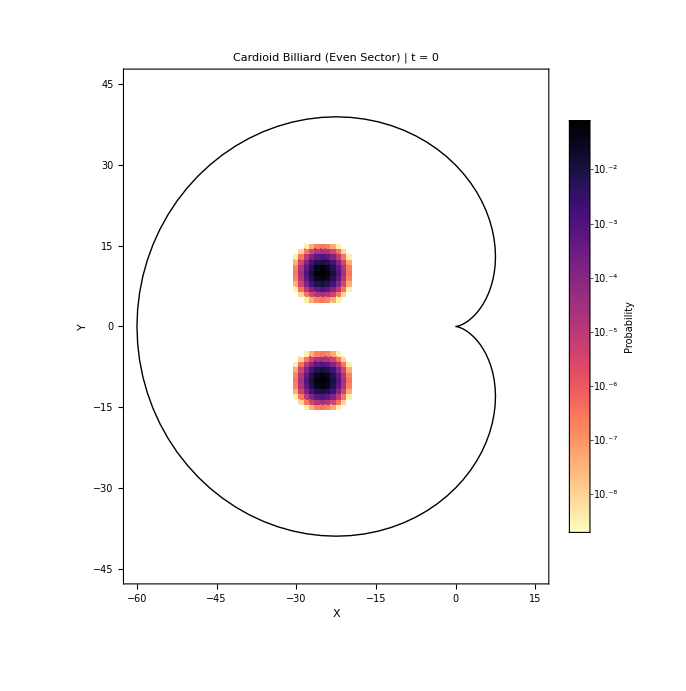

```mathematica
frames[[1]]
```

```mathematica
rasterizedFrames=Rasterize[#,"Image",ImageResolution->144]&/@frames;
```

```mathematica
Do[Export[FileNameJoin@{DirectoryName[videoPath],StringTemplate["frame_``.png"][IntegerString[i,10,4]]},rasterizedFrames[[i]]],{i,Length[rasterizedFrames]}]
```